# Causality : A Brief Introduction

Parth Kashikar

Artificial Intelligence has revolutionized technology. The research in the field has  grown exponentially with the advent of AI-based solutions in almost every field of human study. That being said, most of the models and implementations that we see today, are based on correlation rather than causality. Judea Pearl, Turing Award Winner, known for his significant contributions to probabilistic AI and Bayesian Networks, points out that much of the current common practice in AI "amounts to just curve fitting." By this, he means to say that there have been relatively lesser efforts in the creation of AI that reflects upon causality. In this article, we explore the basic difference between the two, and have a brief discussion about some of the mathematics behind causal modelling.

Data Exploration

First, let’s have a look at the positions of the global tectonic plate boundaries and Earthquake data from 1900 to the present.

```mathematica
p1=GeoGraphics[ResourceData["Large Global Plate Boundaries"][All,"Polygon"]];
p2=GeoHistogram[EarthquakeData[All,6,{{1900,1,1},Now},"Position"],200,ColorFunction->"SolarColors",PlotLegends->Automatic];
Pane[Show[p1,p2], Full, Alignment->Center]
```

EarthquakeData::dupdate: Earthquakes returned with duplicate dates, values may be combined.

-Graphics-

We clearly see that the majority of the Earthquakes around the world are along the joining points of two adjacent plates. This data is expected, and scientific studies have shown that earthquakes occur due to plate-plate collision, shearing stress or other plate-plate interactions. Next up is a really bizarre attempt at showcasing a correlation between Wikipedia hits of the famous Hollywood actor Chris Evans versus Measles Cases in the Democratic Republic of Congo. It is important to note that the data has been appropriately scaled and clipped to amount to a visually correlating plot.

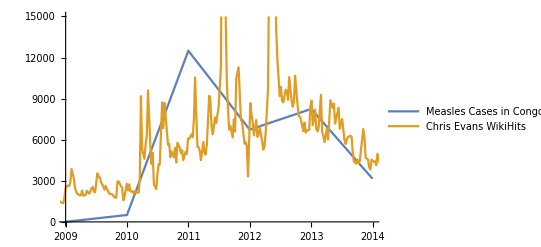

```mathematica
data1= TimeSeries[QuantityMagnitude[WolframAlpha["Chris Evans",{{"PopularityPod:WikipediaStatsData",1},"TimeSeriesData"}]]];
data2=TimeSeries[QuantityMagnitude[ResourceData["Infectious Diseases by Country 2009-2014"][Select[MatchQ[#Country,Entity["Country","DemocraticRepublicCongo"]]&]][All,{"Country","MeaslesCases"}][1,"MeaslesCases"]]];
multiplier = Mean[data2]/Mean[data1];
rescaledData2 = data2*(1/multiplier);
Pane[DateListPlot[{rescaledData2,data1},PlotLegends->{"Measles Cases in Congo","Chris Evans WikiHits"},PlotRangeClipping->True, PlotRange->{{{2009,1,1,0,0,0},{2014,1,1,0,0,0}},{0,15000}},ImageSize->400,Frame->False,Axes->{True,False}],Full,Alignment->Center]
```

Although Chris Evans’ popularity is not a cause of Measles, or vice-versa, the data is still correlated. It is possible to fit a model with these variables as inputs and outputs, but such an application would be meaningless, because such data is clearly not causally linked (as we know from the science behind Measles).  Finally, we look at an analysis done in a publication for the New England Journal of Medicine. Chocolate consumption to Per-Capita Nobel Laureates.

```mathematica
perCapitaData = Import["/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/country-chocolates.xlsx", "Data"];
nobelPrizeData = Flatten[Import["/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/nobel_prize.csv", "Data"]];
nobelPrizeDataClean = Counts[Flatten@StringCases[nobelPrizeData,{a___~~"("~~b__~~")":>b,__}]];
chocolatePerCapita = Association[Rule@@@perCapitaData[[1]]];
countrypop= AssociationThread[CountryData[#,"Name"]&/@CountryData[],CountryData[#,"Population"]&/@CountryData[]];
nobelPerCapita= N@QuantityMagnitude[Divide@@KeyIntersection[{nobelPrizeDataClean,countrypop}]];
nobelPerCapitaFinal = KeySelect[nobelPerCapita,MemberQ[Keys[chocolatePerCapita],#]&];
pairs=Merge[{nobelPerCapitaFinal, chocolatePerCapita}, Identity];
Pane[ListPlot[Select[pairs,Length[#]==2&],PlotStyle->{PointSize[Large],Red},ImageSize->700,AxesLabel->{"NobelPrize PerCapita","ChocolateConsumption PerCapita"}],Full,Alignment->Center]
```

-Graphics-

Here, we are unsure of causality but seem to be able to establish a strong correlation as well. This is the key point the causality research work is trying to make. The big claim here is that causality will be the primary carrier of the “model of reality” to AI models. The next step that could be achieved would then be analysis and refinement of empirical data. A mathematical establishment of causality is the first step into the “future of AI”.

### Introducing Do-Calculus

```mathematica
graphs = List[Graph[{1,2,3,4},{2->1,2->3,3->4,1->4}, VertexSize->Medium,ImageSize->100],
Graph[{1,2,3,4},{1->2,2->4,3->4,1->4,2->3}, VertexSize->Medium,ImageSize->100],
Graph[{1,2,3,4},{1->2,3->2,2->4,1->3}, VertexSize->Medium,ImageSize->100],
Graph[{1,2,3,4},{1->4,3->1,2->3,4->3}, VertexSize->Medium,ImageSize->200],
Graph[{1,2,3,4},{1->3,3->2,4->2,4->3}, VertexSize->Medium,ImageSize->100]];
```

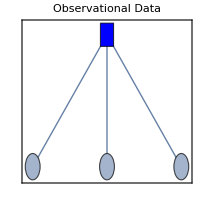
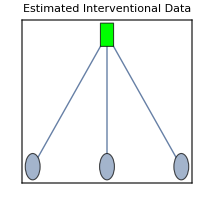
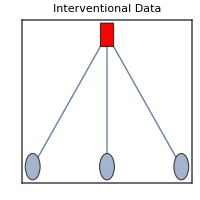
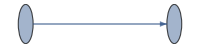
|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
P(Y|x) | P̃(Y,do(x)) | P(Y,do(x))

```mathematica
Pane[Grid[{{"",ListAnimate[graphs,0.7,Paneled->False,Alignment->Center]/.HoldPattern[AppearanceElements->_]->AppearanceElements->None},

{Graph[{1,2,3,4},{1<->2,1<->3,1<->4},VertexShapeFunction->{1->"Square"}, VertexSize->Medium, VertexStyle->{1 -> Blue},VertexSize->Automatic, Frame->True,ImageSize->200, PlotLabel->"Observational Data"],Graph[{1,2,3,4},{1<->2,1<->3,1<->4},VertexShapeFunction->{1->"Square"}, VertexSize->Medium, VertexStyle->{1 -> Green},Frame->True,ImageSize->200,PlotLabel->"Estimated Interventional Data"],
Graph[{1,2,3,4},{1<->2,1<->3,1<->4},VertexShapeFunction->{1->"Square"}, VertexSize->Medium, VertexStyle->{1 -> Red},Frame->True,ImageSize->200, PlotLabel->"Interventional Data"]},

{Graph[{1,2},{2->1},VertexSize->0.1,ImageSize->200],
Graph[{1,2},{2->1},VertexSize->0.1,ImageSize->200],
Graph[{1,2},{2->1},VertexSize->0.1,ImageSize->200]},

{Style["P(Y|x)",Blue,Bold],Style["P̃(Y,do(x))",Green,Bold],Style["P(Y,do(x))",Red,Bold]}}],Full,Alignment->Center]
```

A foray into the problem of causality are the ideas of "Do-Calculus". When talking about causality in AI, we are dealing with 2 probability distributions, namely the observed data and the desired "interventional data".

𝒫 (𝒴 | 𝓍) is the probability distribution that we commonly train our current ML/DL models to fit. It is a conditional distribution which can be calculated from p(x,y,z,…) as a ratio of two of its marginals.

𝒫 (𝒴 | 𝓍) = 𝒫 (𝒴, 𝓍)/(𝒫 (𝓍))

𝒫(𝒴,do(𝓍)) is the probability distribution that is desirable for an establishment of causal models. It is the probability distribution that indicates “what would happen to Y if we were to intervene and set x to a certain value.

For example, let’s consider a pressure chamber with a barometer. The observational data over some experimentation/usage case of this chamber would amount to a simple graphical equation of Y = X.

𝒫(𝒴|𝓍) = {1, y = x
0, y ≠ x

But in the case of the interventional data, if 𝓍 reads 0.5 Bar, and we intervene and change it to 1 Bar, 𝒴 doesn’t change at all! This is because 𝒴 causes 𝓍, and not vice-versa.

𝒫(𝒴|𝓍) = {1, y = x'(pre intervention)
0, y ≠ x

Do calculus establishes the relation between the observational data and an assumed estimation of the interventional data P̃(Y,do(x)). The green joint estimation is understood by an implicit causal graph (drawn above the undirected joint graph). Multiple causal graphs can lead to the same joint distribution, making the relation between them many-one. Do-calculus allows us to massage the green conditional distribution until we can express it in terms of various marginals, conditionals and expectations under the blue distribution. Do-calculus extends our toolkit of working with conditional probability distributions with four additional rules we can apply to conditional distributions with the do operators in them. These rules take into account properties of the causal diagram.  In the case where we are able to express the estimation as a bunch of conditionals and marginals of the observed data, we call it “identifiable”. The data is called “unidentifiable” otherwise.  A typical relation between the two is something as follows:

𝒫̃(𝒴,𝒹ℴ(𝓍)) = 𝔼_(x'~p(x))𝔼_(z~p(z|x)p(y'|x))

The checking of the accuracy of the trained model on a causal framework is questionable as well. The accuracy of the causal graph as well as the model are mostly based on empirical data, which is, in effect, the human involvement to communicate “a model of reality” to the models in consideration. The key take-away here is that without causal data, AI models cannot effectively answer interventional level questions or counter-factual questions. There are areas where fitting on observational data works amazingly well, and deep learning has outperformed previous algorithms, even humans. Unsupervised learning algorithms such as RL have led to great AI applications as well. There are certain areas where causality plays an important role, in fields of healthcare, marketing, strategy formation, and specifically, scientific formalisations. This has been a quick peak into the study behind causality, but it can serve as a start for the study into the field for the reader!

### References, Relevant Links and Further Explorations

An Introduction to Judea Pearl’s Do-Calculus

A quick guide to Do-Calculus

Judea Pearl Interview with Quanta Magazine

Do Storks Deliver Babies?

More Spurious Correlations